# Lagrange Points: Developing an Intuition

When two large objects orbit one-another, there exist equilibrium points around them where small satellites will feel no net force. These locations are called Lagrange points, and they allow satellites to stay in one position (relative to the two objects) while expending a minimal amount of energy. The Lagrange points orbit along with the two bodies.

-Graphics-
By Xander89-File:Lagrange_points2.svg,CC BY 3.0,https://commons.wikimedia.org/w/index.php?curid=36697081

The key to understanding Lagrange points is realizing that objects traveling in orbits experience a Centrifugal force that appears to force the satellite outward. When this outward force balances the inward force of gravity, you get a Lagrange point. In this regard, L1-L3 are generally considered fairly intuitive.

## The Relevant Potentials

We begin by creating the gravitational potential for a single object of mass M, as experienced by a second object of mass m.

```mathematica
gravPotential[M_,m_,G_, objectX_,objectY_,X_,Y_]:=-(G*M*m)/EuclideanDistance[{objectX, objectY}, {X, Y}]
```

```mathematica
Framed[
Column[
{
Style["Single Object Gravitational Potential",Bold,16],
GraphicsRow[
{
Plot3D[gravPotential[1, 1, 1, 0, 0, x, y], {x, -4, 4}, {y, -4, 4}],
ContourPlot[gravPotential[1, 1, 1, 0, 0, x, y], {x, -4, 4}, {y, -4, 4}, ClippingStyle->Automatic]
}
]
},
Alignment->Center],
FrameMargins->10]
```

These potentials are additive, so to make the potential for two objects all we need to do is add them together. 
You’ll notice I’ve done a few things to make working with this data easier:
I’ve set m and G to be 1. I only really care about the general shape of the potential, which these won’t impact.
I’ve constrained the system to lie along the X-axis by setting Y to zero.
I’ve constrained the system such that its center of mass is at the origin by setting M1 to position X1 and M2 to position -M1/M2X1.

```mathematica
m:=1
g:=1
twoGrav[M1_, M2_, X1_, X_, Y_]:=gravPotential[M1, m, g, X1, 0, X, Y] + gravPotential[M2, m, g, -M1/M2 X1, 0, X,  Y]
```

In the image below, you can see an equilibrium point between the two masses, where an object will feel an equal pull towards both objects.

```mathematica
Framed[
Column[
{
Style["Two Object Gravitational Potential",Bold,16],
GraphicsRow[
{
Plot3D[twoGrav[2,1, -1, x, y], {x, -5,5}, {y, -5, 5}, PlotPoints->25],
ContourPlot[twoGrav[2,1, -1, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->3]
}
]
},
Alignment->Center],
FrameMargins->10]
```

```mathematica
centrifugal[w_,m_,x_, y_]:= -1/2 w^2*m*EuclideanDistance[{0,0},{x,y}]
```

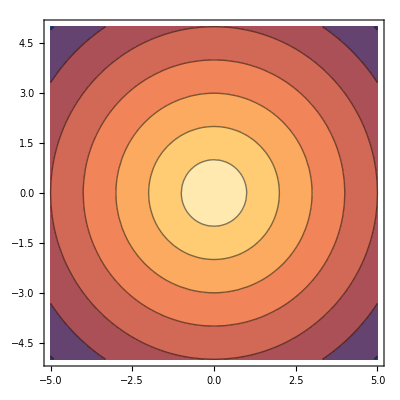

-Graphics3D-

```mathematica
ContourPlot[centrifugal[1, m, x, y],{x,-5,5},{y,-5,5}]
Plot3D[centrifugal[1, m, x, y],{x,-5,5},{y,-5,5}]
```

```mathematica
mass:=0.01
Manipulate[GraphicsColumn[{
GraphicsRow[{
Plot3D[TwoGrav[ratio*mass,mass, -separation, x, y],{x, -5, 5}, {y, -5, 5},PlotRange->{-7*10^-7,-3*10^-8}, Mesh->None, PlotLabel->"Gravitational Potential"],
Plot3D[Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5},PlotRange->{-1.5*10^-7,0}, Mesh->None, PlotLabel->"Centrifugal Potential"]
}],
GraphicsRow[{
Plot3D[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, PlotLabel->"Combined Effective Potential"],
ContourPlot[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->2, Contours->20, PlotLabel->"Combined Effective Potential"]
}]
}],
{spin,0,0.07},{separation,0,3},{ratio,1,3}]
```

```mathematica
mass:=0.01
separation:=0
ratio:=1
Export["spin.gif",Table[
Plot3D[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, PlotLabel->"Combined Effective Potential", LabelStyle->Opacity[0]],
{spin,0,0.07,0.003}]]
```

spin.gif

```mathematica
mass:=0.01
spin:=0.066
ratio:=1
Export["separation.gif",Table[GraphicsRow[{
Plot3D[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, PlotLabel->"Combined Effective Potential", LabelStyle->Opacity[0]],
ContourPlot[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30,Contours->30, Mesh->None, PlotLabel->"Combined Effective Potential", LabelStyle->Opacity[0]]}],
{separation,0,1.5, 0.02}]]
```

separation.gif

```mathematica
mass:=0.01
spin:=0.066
separation:=1.5
Export["ratio.gif",Table[GraphicsRow[{
Plot3D[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30, Mesh->None, PlotLabel->"Combined Effective Potential", LabelStyle->Opacity[0]],
ContourPlot[TwoGrav[ratio*mass,mass, -separation, x, y]+Centrifugal[spin, 0.00001, x, y], {x, -5, 5}, {y, -5, 5}, ClippingStyle->Automatic, MaxRecursion->1, PlotPoints->30,Contours->30, Mesh->None, PlotLabel->"Combined Effective Potential", LabelStyle->Opacity[0]]}],
{ratio,1,5,0.1}]]
```

ratio.gif